## Function defintions

```mathematica
Clear["Global`*"]
$Assumptions = {Element[ym1,Reals],Element[ym2,Reals],Subscript[σ, 1]>0,Subscript[σ, 2]>0,cor>0,Subscript[α, 11]>0,Subscript[α, 11]>Subscript[α, 12]};

gausMat={{Subscript[α, 11],Subscript[α, 12]}, {Subscript[α, 12],Subscript[α, 22]}};
fullGaussMat=gausMat/2;
corMat={{Subscript[σ, 1]^2,cor}, {cor,Subscript[σ, 2]^2}};
Yn = {{Subscript[y, 1]},{Subscript[y, 2]}};
YmVec = {{ym1},{ym2}};
σMat = {{Subscript[σ, 1],0},{0,Subscript[σ, 2]}};
```

## Derivation

### Obtaining α_11

```mathematica
sol11=Simplify[Solve[(Inverse[gausMat])[[1,1]]==((corMat[[1,1]])) ,Subscript[α, 11]]]
```

{{α_11→α_12^2/α_22+1/σ_1^2}}

```mathematica
exprα11=(Subscript[α, 11]/.sol11[[1]])
```

α_12^2/α_22+1/σ_1^2

### Obtaining α_22

```mathematica
sol22=Simplify[Solve[(Inverse[gausMat])[[2,2]]==((corMat[[2,2]])) ,Subscript[α, 22]]]
```

{{α_22→α_12^2/α_11+1/σ_2^2}}

```mathematica
exprα22=(Subscript[α, 22]/.sol22[[1]])
```

α_12^2/α_11+1/σ_2^2

### Obtaining α_12

```mathematica
sol12=Simplify[Solve[(Inverse[gausMat])[[1,2]]==((corMat[[1,2]])) ,Subscript[α, 12]]]
```

{{α_12→-(-1+√(1+4 cor^2 α_11 α_22))/(2 cor)},{α_12→(1+√(1+4 cor^2 α_11 α_22))/(2 cor)}}

Rule out the second solution by the argument that α_12 has to be less than α_11: (1+√(1+4 cor^2 α_11 α_22))/(2cor)>(√(1+4 cor^2 α_11 α_22))/(2cor)>(√(4 cor^2 α_11 α_22))/(2cor)=√(α_11 α_22) Visually, this can be seen as well

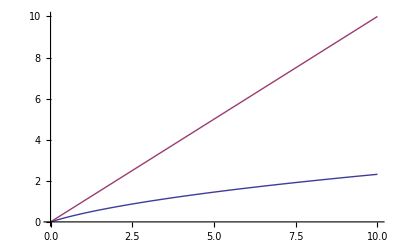

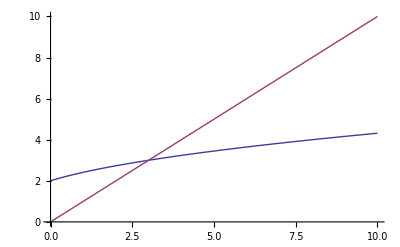

```mathematica
Plot[{Abs[(Subscript[α, 12]/.sol12[[1]])/.{ym-> 0,cor-> 0.5,Subscript[α, 22]-> 1}],Subscript[α, 11]},{Subscript[α, 11],0,10}]
Plot[{(Subscript[α, 12]/.sol12[[2]])/.{ym-> 0,cor-> 0.5,Subscript[α, 22]-> 1},Subscript[α, 11]},{Subscript[α, 11],0,10}]
```

```mathematica
exprα12=(Subscript[α, 12]/.sol12[[1]])
```

-(-1+√(1+4 cor^2 α_11 α_22))/(2 cor)

### Combining results: Expressing α in terms of the correlation matrix

```mathematica
sol=Simplify[Solve[{Subscript[α, 11]==(exprα11),Subscript[α, 12]==(exprα12),Subscript[α, 22]==(exprα22)},{Subscript[α, 11],Subscript[α, 12],Subscript[α, 22]}]]
```

{{α_11→σ_2^2/(-cor^2+σ_1^2 σ_2^2),α_12→cor/(cor^2-σ_1^2 σ_2^2),α_22→σ_1^2/(-cor^2+σ_1^2 σ_2^2)}}

### Simplifying the argument inside the exponential

Without variable transformation

```mathematica
exprInExp = -Transpose[Yn-YmVec].fullGaussMat.(Yn-YmVec);
exprInExp = Simplify[exprInExp];
exprInExp=(exprInExp/.sol)[[1,1]];
exprInExp = Simplify[Expand[exprInExp[[1]]]];
exprInExp = FullSimplify[exprInExp/.{cor-> ρ*Subscript[σ, 1]*Subscript[σ, 2]}]
```

((ym2-y_2)^2 σ_1^2-2 ρ (ym1-y_1) (ym2-y_2) σ_1 σ_2+(ym1-y_1)^2 σ_2^2)/(2 (-1+ρ^2) σ_1^2 σ_2^2)

Write the above in a more neat form

```mathematica
tempExpr = 0;
nIndex=1;
While[(FullSimplify[tempExpr-exprInExp]===0)==False,
tempExpr=Normal[Series[exprInExp,{Subscript[y, 1],ym1,nIndex},{Subscript[y, 1],ym1,nIndex}]];

nIndex=nIndex+1;
]

tempExpr
Simplify[((-ym1+Subscript[y, 1]) (ym2 ρ-ρ Subscript[y, 2]))/((-1+ρ^2) Subscript[σ, 1] Subscript[σ, 2])]
```

(-ym1+y_1)^2/(2 (-1+ρ^2) σ_1^2)+(ym2-y_2)^2/(2 (-1+ρ^2) σ_2^2)+((-ym1+y_1) (ym2 ρ-ρ y_2))/((-1+ρ^2) σ_1 σ_2)

(ρ (-ym1+y_1) (ym2-y_2))/((-1+ρ^2) σ_1 σ_2)

And so we can write that the argument in the exponential is equal to (-ym1+y_1)^2/(2 (-1+ρ^2) σ_1^2)+(ym2-y_2)^2/(2 (-1+ρ^2) σ_2^2)+((-ym1+y_1) (ym2 ρ-ρ y_2))/((-1+ρ^2) σ_1 σ_2)=-((y_1-ym1)^2/(2 (1-ρ^2) σ_1^2)+(y_2-ym2)^2/(2 (1-ρ^2) σ_2^2)-(ρ(y_1-ym1) ( y_2-ym2))/((1-ρ^2) σ_1 σ_2))

Compare

```mathematica
exprToCompare=-1/2*Transpose[Yn-YmVec].Inverse[corMat].(Yn-YmVec);
exprToCompare=exprToCompare[[1,1]]/.{cor-> ρ*Subscript[σ, 1]*Subscript[σ, 2]};

tempExpr = 0;
nIndex=1;
While[(FullSimplify[tempExpr-exprToCompare]===0)==False,
tempExpr=Normal[Series[exprToCompare,{Subscript[y, 1],ym1,nIndex},{Subscript[y, 1],ym1,nIndex}]];

nIndex=nIndex+1;
]
tempExpr
```

(-ym1+y_1)^2/(2 (-1+ρ^2) σ_1^2)+(ym2-y_2)^2/(2 (-1+ρ^2) σ_2^2)+(ρ (-ym1+y_1) (ym2-y_2))/((-1+ρ^2) σ_1 σ_2)

Hence, we obtain that -(Y-Ym)^T C^-1(Y-Ym)=(-ym1+y_1)^2/(2(-1+ρ^2) σ_1^2)+(ym2-y_2)^2/(2(-1+ρ^2) σ_2^2)+(ρ (-ym1+y_1) (ym2-y_2))/((-1+ρ^2) σ_1 σ_2)
=-((y_1-ym1)^2/(2(1-ρ^2) σ_1^2)+(y_2-ym2)^2/(2(1-ρ^2) σ_2^2)-(ρ (y_1-ym1) (y_2-ym2))/((1-ρ^2) σ_1 σ_2))
which was what obtained in full answer.

### With variable transformation

With variable transformation

```mathematica
exprInExp = -Transpose[σMat.Yn].fullGaussMat.(σMat.Yn);
exprInExp = Simplify[exprInExp];
exprInExp=(exprInExp/.sol)[[1,1]];
exprInExp = Simplify[Expand[exprInExp[[1]]]];
exprInExp = FullSimplify[exprInExp/.{cor-> ρ*Subscript[σ, 1]*Subscript[σ, 2]}]
```

(y_1^2-2 ρ y_1 y_2+y_2^2)/(2 (-1+ρ^2))

Normalization constant

```mathematica
testExpr=Exp[-(y1^2+y2^2-2*C21*y1*y2)/2/(1-C21^2)];
step1=Assuming[C21<1,Integrate[testExpr,{y1,-Infinity,Infinity}]]
step1=Assuming[C21<1,Integrate[step1,{y2,-Infinity,Infinity}]]
```

ConditionalExpression[√(1-C21^2) ⅇ^(-y2^2/2) √(2 π),C21>-1]

ConditionalExpression[2 √(1-C21^2) π,C21>-1]

Verification

```mathematica
testExpr=Exp[-(y1^2+y2^2-2*C21*y1*y2)/2/(1-C21^2)];
step1=Assuming[C21<1,Integrate[y1*y2*testExpr,{y1,-Infinity,Infinity}]]
step1=Assuming[C21<1,Integrate[step1,{y2,-Infinity,Infinity}]]
```

ConditionalExpression[C21 √(1-C21^2) ⅇ^(-y2^2/2) √(2 π) y2^2,C21>-1]

ConditionalExpression[2 C21 √(1-C21^2) π,C21>-1]